```mathematica
data1={40.5,40.6,40.25,40.4,40.3,40.35,40,39.8, 40.45,40.6,40.65,40.7,40.75,40.8,40.85,40.9,40.95,41,41.05,40.1};
data2=Abs[{2,3.7,17.6,12.4,16.5,15,20.2,21.1,8.33.6,9,12.6,15,16.5,17.6,18.4,19,19.5,19.9,20.2}-23.5];
datac=Partition[Riffle[data1,data2],2]
```

{{40.5,21.5},{40.6,19.8},{40.25,5.9},{40.4,11.1},{40.3,7.},{40.35,8.5},{40,3.3},{39.8,2.4},{40.45,18.502},{40.6,14.5},{40.65,10.9},{40.7,8.5},{40.75,7.},{40.8,5.9},{40.85,5.1},{40.9,4.5},{40.95,4.},{41,3.6},{41.05,3.3}}

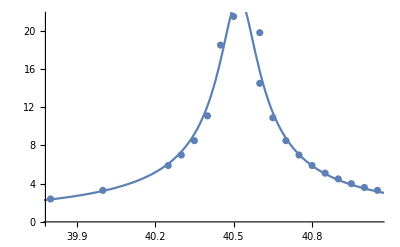

```mathematica
amp=23.5;
freq0=40.52;
qq=280;
Show[ListPlot[datac],Plot[((amp*freq0)/(2*qq))/Sqrt[((x-freq0)^2+((freq0/(2*qq))^2))],{x,25,55}, PlotRange->All]]
```

```mathematica
fit=NonlinearModelFit[datac,((amp1*freq01)/(2*qq1))/Sqrt[((x-freq01)^2+((freq01/(2*qq1))^2))],{{amp1,5},{qq1,50},{freq01,40}},x]
```

FittedModel[1.70749/(√(0.00513083+(-«18»+x)^2))]

```mathematica
fit[{"BestFit","ParameterTable"}]
```

{1.70749/(√(0.00513083+(-40.5251+x)^2)), | Estimate | Standard Error | t-Statistic | P-Value
amp1 | 23.8378 | 1.37255 | 17.3675 | 8.32975×10^-12
qq1 | 282.879 | 27.0849 | 10.4442 | 1.49547×10^-8
freq01 | 40.5251 | 0.00480229 | 8438.7 | 1.2754×10^-54}

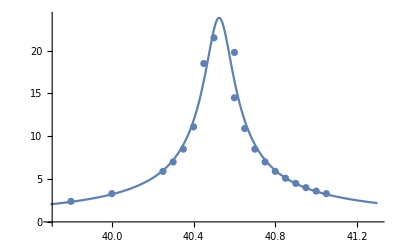

```mathematica
Show[ListPlot[datac,PlotRange->{{39.7,41.3},{0,24}}],Plot[fit[x],{x,39.7,41.3}]]
```